```mathematica
r[x_]:= x+ r0
r0 = 1/(4c);
Veff[x_] := 1/(8r[x]^2) -c/r[x] + 2c^2
```

```mathematica
phiminusone[x_]:= Assuming[x>=0&&c>=0,Simplify[-Sqrt[Simplify[2Veff[x]]]]]
pot[x_] := -c k^2Exp[-b*25*r[x]/k^2]/r[x]
Eminustwo = -2c^2;
```

```mathematica
Eminusone = D[x(-phiminusone[x])some[x]-x(1/2  D[phiminusone[x],x]+1/(2r[x]^2))-phiminusone[x],x] /.x->0;
phizero =Simplify[(x (Eminusone +1/2  D[phiminusone[x],x]+1/(2r[x]^2))+ phiminusone[x])/ (x(-phiminusone[x]))];
COne = phizero /(Eminusone+1/2D[phiminusone[x],x]+ phiminusone[x]phizero+1/(2r[x]^2)) /. x->0;
Ezero = D[-x(1/2D[phizero,x]+1/2 phizero^2-3/(8r[x]^2)-SeriesCoefficient[pot[x],{k,Infinity,0}] )+COne(Eminusone+1/2D[phiminusone[x],x]+ phiminusone[x]phizero+1/(2r[x]^2))-phizero ,x] /. x->0;
phione = Simplify[(x(Ezero +1/2D[phizero,x]+1/2 phizero^2-3/(8r[x]^2)-SeriesCoefficient[pot[x],{k,Infinity,0}]) -COne(Eminusone+1/2D[phiminusone[x],x]+ phiminusone[x]phizero+1/(2r[x]^2))+phizero) / (x(-phiminusone[x]))];
Ctwo =( -COne(Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero[x]^2-25c*b-3/(8r[x]^2))+phione)/(Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)) /.x->0;
Eone = D[-x(1/2 D[phione,x]+ phione*phizero) +COne(Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero[x]^2-25c*b-3/(8r[x]^2))+Ctwo((Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)))-phione,x] /. x->0;
phitwo = Simplify[(x(Eone+1/2 D[phione,x]+ phione*phizero) -COne(Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero[x]^2-25c*b-3/(8r[x]^2))-Ctwo((Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)))+phione)/ (x(-phiminusone[x]))];
```

```mathematica
phi[n_] := phi[n] = Which[n==-1,phiminusone[x],n==0, phizero, n==1, phione, n==2, phitwo,True,Simplify[ (x(1/2 D[phi[n-1],x]+Energy[n-1]+ 1/2Sum[phi[m]phi[n-m-1],{m,0,n-1}]+ termone[n])-
Sum[Cs[m](Energy[n-m-1]+1/2D[phi[n-1-m],x]+1/2Sum[phi[p]phi[n-m-p-1] ,{p,-1,n-m}]+termtwo[n,m]),{m,1,n-2}]-Cs[n-1](Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero^2-25c*b-3/(8r[x]^2))-Cs[n] (Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2))+phi[n-1])/(-x*phiminusone[x])]]
Cs[n_]:= Cs[n] = Which [n==1,COne,n== 2,Ctwo,True,Simplify[(-Sum[Cs[m](Energy[n-m-1]+1/2D[phi[n-m-1],x]+1/2Sum[phi[p]phi[n-m-p-1] ,{p,-1,n-m}]+termtwo[n,m]),{m,1,n-2}]-Cs[n-1](Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero^2-25c*b-3/(8r[x]^2))+phi[n-1])/(Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)) /. x->0]]
Energy[n_]:= Energy[n]= Which[n==-2,Eminustwo,n==-1,Eminusone,n==0,Ezero,n==1,Eone,True,Simplify[D[-x(1/2 D[phi[n],x]+ 1/2Sum[phi[m]phi[n-m],{m,0,n}]+ termone[n+1])+
Sum[Cs[m](Energy[n-m]+1/2D[phi[n-m],x]+1/2Sum[phi[p]phi[n-m-p] ,{p,-1,n-m+1}]+termtwo[n+1,m]),{m,1,n-1}]+Cs[n](Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero^2-25c*b-3/(8r[x]^2))+Cs[n+1] (Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2))-phi[n],x] /. x->0]]
termtwo[n_,m_] := Which[EvenQ[m]&& EvenQ[n] ||OddQ[m]&& OddQ[n],0,True,(-1)^((n-m+1)/2) (25b)^((n-m+1)/2 )/Factorial[((n-m+1)/2) ] *c*r[x]^(((n-m-1)/2) )]
termone[n_]:= Which[EvenQ[n],0,True, (-1)^((n+1)/2)(25b)^((n+1)/2)/Factorial[(n+1)/2]c r[x]^((n-1)/2)]
```

```mathematica
Clear[Energy,phi,Cs]
```

```mathematica
Clear[c]
c = 1/25
```

1/25

```mathematica
k=5
```

5

```mathematica
Energy[117]
```

(56629703796845321410600648568300638169179592883940580311842870129018228364189349511464151291300894895767552+500503617331526869075265087139554238081361179206656381007149572493626218838511298316795716673368588089942932128906250000000000000000000000000000000000000000000000000000000000000000000000000000000000 b^31-5325759222714075901414188510863951677099267412078058705439741983876518833937895761912118429155430305854679318144917488098144531250000000000000000000000000000000000000000000000000000000000000000000000000000 b^32+3726197376919833811157526276601263599127258985729989496645354671048774004430707464224766192919978679007897426345152780413627624511718750000000000000000000000000000000000000000000000000000000000000000000000000000 b^33-499158971275742414011328995830502639831418218717259966466433978709309357815174165483160864325349627907554839190140683058416470885276794433593750000000000000000000000000000000000000000000000000000000000000000000000000 b^34+19791400662992566098188232608307243349269111241400326810723383322677391275255048442041017561695261866566944902777816506223018677701475098729133605957031250000000000000000000000000000000000000000000000000000000000000000000 b^35-294443346812102583875874776165674941216634163364941330087871211904922550722665591377608152913097324381541865581318555798728819894449770799838006496429443359375000000000000000000000000000000000000000000000000000000000000000000 b^36+1905878453294723946003071701893809944368523627640156535110776084369319390677487221006103491110265566489471578035385732475918973971573677772539667785167694091796875000000000000000000000000000000000000000000000000000000000000000000 b^37-5932138778557664297112127239676355841519994612078090894354626114696903309087857969781206811115223791800460162082156193374389717876300764931585263184388168156147003173828125000000000000000000000000000000000000000000000000000000000000 b^38+9534931178195212437282200346529031982906912211550030147248809894096444915645699285824143442751563737464097350065286694262700317721001596130148136865045671584084630012512207031250000000000000000000000000000000000000000000000000000000000 b^39-8343115043161051105992911680308744905142449546248230248387039183680793602404696729060117136261377708634342789699639156286180222125635453592901180641661085246596485376358032226562500000000000000000000000000000000000000000000000000000000000 b^40+4137093032625205298864518686060315699498000204026602997486844187649587329220154100827281237276747173261076816851900136816390914211593765060097200821943863591201306917355395853519439697265625000000000000000000000000000000000000000000000000000 b^41-1199593715245725454222662653305869329664844631044301051292058716251475793651307868633793153869727717103713236126865753980910485543407032709997362791506676088504335098150477278977632522583007812500000000000000000000000000000000000000000000000000 b^42+208544709001311257325894796450345263501804414535196265052656262696733056654849986419797036111095442301718941855562152572468325504225892041199775620005998402457878665439139354020881000906229019165039062500000000000000000000000000000000000000000000 b^43-22182899382238008458514436757931085306832718912793221991282821466553754997316955082263908017800267152109065804058558082185149758827905595612369462304854845120635406779258103071583718701731413602828979492187500000000000000000000000000000000000000000 b^44+1468243914121161519319531011702814531396376502926700814281049726016667884516513234082765528631231958981770926817106145278868721541965604762384658890609687547016532459254190001729512005113065242767333984375000000000000000000000000000000000000000000000 b^45-61327672848716388977016236759682035845448123639364012310846700681313929710030201348033243113948307421201847728478393781452337561483378378211453690731255879989395131773291698629169133027971838600933551788330078125000000000000000000000000000000000000000 b^46+1635725577599402564807547131171071914422443927994090749536658901428622432697985703283934324722394415882611325156464588597163094854108218762327703486204403268853391811485382115924983037480444636457832530140876770019531250000000000000000000000000000000000 b^47-28127663372351815932424194489112685599328116587512260747724320697494172891946509230692071606625855562335413896749393872122679232271215461215227487125737552105780572125565038274167949539777966450060375791508704423904418945312500000000000000000000000000000 b^48+314108361938850410337051351628203305059373892990994333421981596401259239580843396735855633573473527295523834800613006047805201007647005039462049906099358626163717017291074286918554317894064498162265408609528094530105590820312500000000000000000000000000000 b^49-2288010289985010465323532768888361341360232534829523954781321258547750041121685491004182479525568929526921335540523051609100741012857288047985088397140758239148695333937251970822060486744631280231487835408188402652740478515625000000000000000000000000000000 b^50+10877621792533588580199206719069062773196241749037839420576436198446767922150076859732050937438202298488913452210967828916839393024216826548420191356216671900970084209541617228244128267412643359945967347357509424909949302673339843750000000000000000000000000 b^51-33595927020290421303943083289513523306498917636659744470957321302314233457055892571525466676247279361878588303751670057013511502043815776551929137720373961191956314081373107316471446964386540681019033272036722337361425161361694335937500000000000000000000000 b^52+66592006894770644392894270285228505849532953180136223721928412674172741084413885704237809918812122760506599502255101413153214838242381545884411909626259965281956386776624996509003619228309564638350597637339589596194855403155088424682617187500000000000000000 b^53-82763663106247548828515714683599588293435552131486875823375201267324026579984256394818891452833804841151007793701014510670127003542612502693470489330077566827734941474574899456081131913925068066117336274857552158579210299649275839328765869140625000000000000 b^54+61964786545925377994836219877719531136190693653618626543193565756522426366155716173027471399750770663485528651123326898605591167290014826067342394948513293180429085034696661912271684790170110504744718652250790036362104729050770401954650878906250000000000000 b^55-26136816837660606215735599066797648259489589257064732921155707946045206887737450189253095622927195424160723069224652378870313788024856767877645009287059695441018887503237776720754907767356880402971556261537493769109286034790784469805657863616943359375000000 b^56+5538818754398254335833319481843923604370895665859371308597085608818611145466932210045262458478378964065515398077931184019068575601104735814976296865173871221092980924870259561757227780263538261277961746632152780639435363241318555083125829696655273437500000 b^57-475275385096200645697773807171122629660944564923318982221293879176033499324699645759603838740571050623103731794395910263963455534667159323124497265021294405744197306556766017374077494601925260753466188768157399922864581043313592090271413326263427734375000 b^58+9371546002152774428379657479567727272125266971730538922420419468364180200735365337187041059327146231320816497817397619654929365562626476286761503660427399039400533673439246010158462931416272404115008088055385304486477604513083861093036830425262451171875 b^59)/147473186970951357840105855646616245232238523135261927895424140960984969698409764352771227321096080457728000

```mathematica
perturbationorder=10
```

10

```mathematica
perturbationorder=30
maxkOrder = 116
```

30

116

```mathematica
EnergySeries = Collect[Sum[k^(-n)Energy[n],{n,-2,maxkOrder}]+O[b]^(perturbationorder+1),b];
EnergySeriesplusOne= Normal[Collect[Simplify[Collect[Collect[Sum[k^(-n)Energy[n],{n,-2,maxkOrder+1}],k],b]],b]+O[b]^(perturbationorder+1)];
Coefficients = {-2/(k+1)^2};
Do[AppendTo[Coefficients,Collect[Coefficient[EnergySeries, b,n],k] ],{n,1,perturbationorder}]
Coefficientstwo = {-2/(k+1)^2};
Do[AppendTo[Coefficientstwo,Collect[Coefficient[EnergySeriesplusOne, b,n],k] ],{n,1,perturbationorder}]
Table[Coefficients[[n]] -Coefficientstwo[[n]],{n,1,perturbationorder+1}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Simplify[Sum[1/k^2 (-1)^(n+1)(4+2(n-1))/k^n,{n,1,Infinity}] -2/k^2 /. k->l]
```

-2/(1+l)^2

```mathematica
(*Table[Length[Coefficients[[n]] /. Sum ->List],{n,1,perturbationorder+1}]*)
```

```mathematica
k=3
```

3

```mathematica
PartialSum = Table[Total[Take[Coefficients,order+1]*Table[b^n,{n,0,order}]],{order,0,perturbationorder}];
```

```mathematica
value = 0.05
N[PadeApproximant[Simplify[PartialSum[[perturbationorder+1]] ] ,{b,0,Floor[perturbationorder/2]}] /. b->value]
```

0.05

-0.0185578

```mathematica
NumberForm[-0.05070822417583923,16]
```

-0.05070822417583923

```mathematica
0.02
```

0.02

```mathematica
k
```

5

```mathematica
NumberForm[-0.012107865770455367,16]
```

-0.01210786577045537

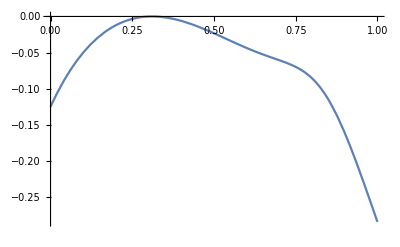

```mathematica
Plot[N[PadeApproximant[Simplify[PartialSum[[perturbationorder+1]] ] ,{b,0,Floor[perturbationorder/2]}] /. b->s],{s,0,1}]
```

```mathematica
N[PartialSum[[perturbationorder+1]]/a^2 /. g->0.3]
```

-1.75384×10^11

```mathematica
NMaximize[function[s],s]
```

{-1.77418×10^-10,{s→0.310209}}

```mathematica
function[s_] := Which[s>= 0 && s<=0.5, N[PadeApproximant[Simplify[PartialSum[[perturbationorder+1]] ] ,{b,0,Floor[perturbationorder/2]}] /. b->s],True,-1]
```

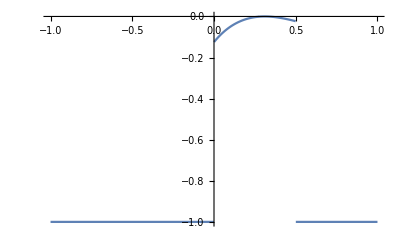

```mathematica
Plot[function[s],{s,-1,1}]
```

```mathematica
k=3
```

3

```mathematica
N[function[0.31]]
```

-3.81678×10^-8

```mathematica
NumberForm[-0.1152932851679943,16]
```

-0.1152932851679943

```mathematica
Clear[k]
```

```mathematica
Clear[k]
```

```mathematica
Coefficients
```

{-1/18,1,-25/4,30,-2295/8,29403/8,-449307/8,7672725/8,-9115776855/512,45060827715/128,-37495774897443/5120}

```mathematica
List
```

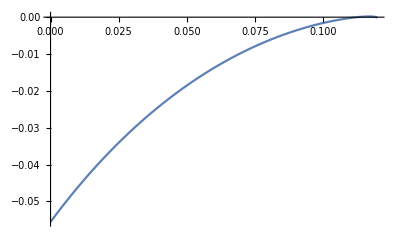

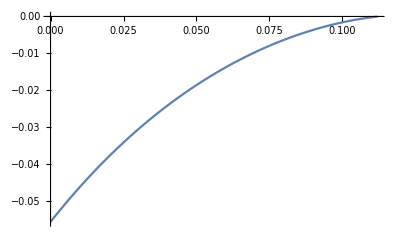

```mathematica
Plot[N[PadeApproximant[Simplify[PartialSum[[perturbationorder+1]] ] ,{b,0,Floor[perturbationorder/2]}] /. b->x],{x,0,0.12}]
```

```mathematica
Export["yukawa3pE.txt",list,"Table","FieldSeparators"->" "]
```

yukawa3pE.txt